```mathematica
Clear[x1,x2,sol]
sol=DSolve[{-k(x1[t]-x2[t])-(mg/l)x1[t]==m*x1''[t],k(x1[t]-x2[t])-(mg/l)x2[t]==m*x2''[t],x1[0]==0.1,x2[0]==0.1,x1'[0]==0,x2'[0]==0},{x1,x2},t]
```

{{x1→Function[{t},0.05 ⅇ^(-(√(-20-mg) t)/(√2)-(ⅈ √mg t)/(√2)) (1. ⅇ^((√(-20-mg) t)/(√2))+1. ⅇ^((√(-20-mg) t)/(√2)+ⅈ √2 √mg t))],x2→Function[{t},0.05 ⅇ^(-(√(-20-mg) t)/(√2)-(ⅈ √mg t)/(√2)) (1. ⅇ^((√(-20-mg) t)/(√2))+1. ⅇ^((√(-20-mg) t)/(√2)+ⅈ √2 √mg t))]}}

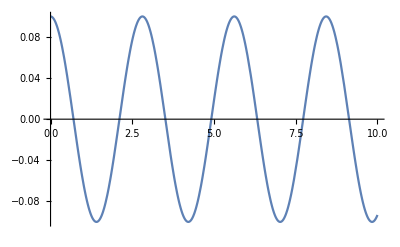

```mathematica
Plot[0.05 ⅇ^(-(√(-20-10) t)/(√2)-(ⅈ √10 t)/(√2)) (1. ⅇ^((√(-20-10) t)/(√2))+1. ⅇ^((√(-20-10) t)/(√2)+ⅈ √2 √10 t)),{t,0,10}]
```